## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGK";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:\MASSef";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PGK_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:E:\Dropbox (UCSD SBRG)\Kinetics (Dan)\Notebooks_for_Grad_Project\Enzyme modules\Glycolysis\PGK\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGK[c] + 13dpg[c] <=> E_PGK[c]&13dpg",
				"E_PGK[c]&13dpg + adp[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c] + adp[c] <=> E_PGK[c]&adp",
				"E_PGK[c]&adp + 13dpg[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp",

				"E_PGK[c]&3pg&atp <=> E_PGK[c]&3pg + atp[c]",
				"E_PGK[c]&3pg <=> E_PGK[c] + 3pg[c]",
				
				"E_PGK[c]&3pg&atp <=> E_PGK[c]&atp + 3pg[c]",
				"E_PGK[c]&atp <=> E_PGK[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1,((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2,((PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c)^PGK3,((PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c)^PGK4,((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5,((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c)^PGK7,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c)^PGK8,((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet2={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSet3={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9,  Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet4={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2, catalyticReactionsSet3, catalyticReactionsSet4};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGK^c&(13dpg)^c&adp^c)_^-((PGK^c&(3pg)^c&atp^c)_^)/K_PGK9) Volume_c k_PGK9^⟶}

Volume_c (-(PGK^c&(3pg)^c&atp^c)_^ k_PGK9^⟵+(PGK^c&(13dpg)^c&adp^c)_^ k_PGK9^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Set::shape: Lists {allFittingData,dataPathList,fileList,fileListSub} and RowBox[{"simulateData", "[", RowBox[{TagBox[DynamicModuleBox[{Typeset`var$$ = 1}, InterpretationBox[TagBox[PanelBox[GridBox[{{ItemBox[PopupMenuBox[Dynamic[Typeset`var$$], {1 -> "\"Overview\"", 2 -> "\"Stoichiometry matrix\"", 3 -> "\"Reactions\"", 4 -> "\"Rates\"", 5 -> "\"ODE\"", 6 -> "\"Constraints\"", 7 -> "\"Initial conditions\"", 8 -> "\"Parameters\"", 9 -> "\"GPR\"", 10 -> "\"Pathway map\"", 11 -> "\"Nullspace\"", 12 -> "\"Left Nullspace\"", 13 -> "\"Notes\"", 14 -> "\"Preset Pathways\""}, Enabled -> Automatic, MenuStyle -> {}, DefaultMenuStyle -> "MenuViewLabel"], Alignment -> Left, StripOnInput -> False]}, {ItemBox[StyleBox[PaneSelectorBox[{1 -> PaneBox[StyleBox[TagBox[GridBox[{{"\"Number of species(rows):\"", "11"}, {"\"Number of columns(reactions):\"", "9"}, {"\"Number of exchange reactions:\"", "0"}, {"\"Number of irreversible reactions:\"", "0"}, {"\"Matrix rank:\"", "7"}, {"\"Dimensions null space: \"", "2"}, {"\"Dimensions left null space: \"", "4"}, {"\"Number of parameters\"", "1"}, {"\"Number of custom rate equations\"", "0"}, {"\"Number of equilibrium constants:\"", "0"}, {"\"Number of forward rate constants:\"", "0"}, {"\"Number of initial concentrations:\"", "0"}, {"\"Number of genes:\"", "0"}, {"\"Number of proteins:\"", "0"}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 2 -> TemplateBox[{GraphicsBox[RasterBox[{{{1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}}, {{1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 0., 0.}, {0., 1., 0.}}, {{1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}}, {{1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}}, {{1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}}, {{1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}}, {{1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}}, {{0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}}, {{1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}}, {{1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}}, {{1., 0., 0.}, {1., 0., 0.}, {0., 1., 0.}, {0., 1., 0.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}, {1., 1., 1.}}}, {{0, 0}, {9, 11}}, {0, 1}], BaseStyle -> {FontFamily -> "Helvetica", FontSize -> Scaled[0.015]}, Frame -> True, FrameLabel -> {None, None}, FrameTicks -> {{{{9.5, FormBox["2", TraditionalForm]}, {7.5, FormBox["4", TraditionalForm]}, {5.5, FormBox["6", TraditionalForm]}, {3.5, FormBox["8", TraditionalForm]}, {1.5, FormBox["10", TraditionalForm]}}, {{10.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {9.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {8.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {7.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {6.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {5.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {4.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]], Annotation[#1, (13dpg)^c, "Tooltip"] & ], TraditionalForm]}, {3.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]], Annotation[#1, adp^c, "Tooltip"] & ], TraditionalForm]}, {2.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]], Annotation[#1, atp^c, "Tooltip"] & ], TraditionalForm]}, {1.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {0.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]], Annotation[#1, (3pg)^c, "Tooltip"] & ], TraditionalForm]}}}, {{{0.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK1\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["adp", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["adp", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {1.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK2\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["13dpg", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["13dpg", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {2.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK3\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["atp", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["atp", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {3.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK4\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK4", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK4", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["3pg", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK4", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK4", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["3pg", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {4.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK5\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK5", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK5", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["13dpg", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK5", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK5", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["13dpg", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {5.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK6\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK6", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK6", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["adp", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK6", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK6", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["adp", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {6.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK7\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK7", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK7", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["3pg", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK7", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK7", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["3pg", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {7.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK8\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK8", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK8", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["atp", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK8", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK8", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["atp", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {8.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"PGK9\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK9", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK9", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK9", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK9", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}}, {{0.5, FormBox["1", TraditionalForm]}, {1.5, FormBox["2", TraditionalForm]}, {2.5, FormBox["3", TraditionalForm]}, {3.5, FormBox["4", TraditionalForm]}, {4.5, FormBox["5", TraditionalForm]}, {5.5, FormBox["6", TraditionalForm]}, {6.5, FormBox["7", TraditionalForm]}, {7.5, FormBox["8", TraditionalForm]}, {8.5, FormBox["9", TraditionalForm]}}}}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], ImageSize -> {{800}, {450}}, Method -> {"AxisPadding" -> Scaled[0.02], "DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, "DefaultPlotStyle" -> Automatic, "DomainPadding" -> Scaled[0.02], "RangePadding" -> Scaled[0.05]}], FormBox[FormBox[TemplateBox[{"\"\\!\\(\\*SubscriptBox[\\(S\\), \\(i, j\\)]\\) = 0\"", "\"\\!\\(\\*SubscriptBox[\\(S\\), \\(\\(i\\)\\(,\\)\\(j\\)\\(\\\\ \\)\\)]\\)> 0\"", "\"\\!\\(\\*SubscriptBox[\\(S\\), \\(\\(i\\)\\(,\\)\\(j\\)\\(\\\\ \\)\\)]\\)< 0\""}, "SwatchLegend", DisplayFunction -> (FormBox[StyleBox[StyleBox[PaneBox[TagBox[GridBox[{{TagBox[GridBox[{{GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], GrayLevel[1]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #1}, {GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], RGBColor[0, 1, 0]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #2}, {GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], RGBColor[1, 0, 0]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #3}}, GridBoxAlignment -> {"Columns" -> {Center, Left}, "Rows" -> {{Baseline}}}, AutoDelete -> False, GridBoxDividers -> {"Columns" -> {{False}}, "Rows" -> {{False}}}, GridBoxItemSize -> {"Columns" -> {{All}}, "Rows" -> {{All}}}, GridBoxSpacings -> {"Columns" -> {{0.5}}, "Rows" -> {{0.5}}}], "Grid"]}}, GridBoxAlignment -> {"Columns" -> {{Left}}, "Rows" -> {{Top}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{0}}}], "Grid"], Alignment -> Left, AppearanceElements -> None, ImageMargins -> {{5, 5}, {5, 5}}, ImageSizeAction -> "ResizeToFit"], LineIndent -> 0, StripOnInput -> False], {FontFamily -> "Arial"}, Background -> Automatic, StripOnInput -> False], TraditionalForm] & ), InterpretationFunction :> (RowBox[{"SwatchLegend", "[", RowBox[{RowBox[{"{", RowBox[{InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {GrayLevel[1], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> GrayLevel[0.6666666666666666], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"GrayLevel", "[", "1", "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = GrayLevel[1]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["GrayLevelColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], GrayLevel[1], Editable -> False, Selectable -> False], ",", InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[0, 1, 0], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> RGBColor[0., 0.6666666666666666, 0.], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"RGBColor", "[", RowBox[{"0", ",", "1", ",", "0"}], "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[0, 1, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], RGBColor[0, 1, 0], Editable -> False, Selectable -> False], ",", InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[1, 0, 0], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> RGBColor[0.6666666666666666, 0., 0.], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"RGBColor", "[", RowBox[{"1", ",", "0", ",", "0"}], "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[1, 0, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], RGBColor[1, 0, 0], Editable -> False, Selectable -> False]}], "}"}], ",", RowBox[{"{", RowBox[{#1, ",", #2, ",", #3}], "}"}]}], "]"}] & ), Editable -> True], TraditionalForm], TraditionalForm]}, "Legended", DisplayFunction -> (GridBox[{{TagBox[ItemBox[PaneBox[TagBox[#1, "SkipImageSizeLevel"], Alignment -> {Center, Baseline}, BaselinePosition -> Baseline], DefaultBaseStyle -> "Labeled"], "SkipImageSizeLevel"], ItemBox[#2, DefaultBaseStyle -> "LabeledLabel"]}}, GridBoxAlignment -> {"Columns" -> {{Center}}, "Rows" -> {{Center}}}, AutoDelete -> False, GridBoxItemSize -> Automatic, BaselinePosition -> {1, 1}] & ), InterpretationFunction -> (RowBox[{"Legended", "[", RowBox[{#1, ",", RowBox[{"Placed", "[", RowBox[{#2, ",", "After"}], "]"}]}], "]"}] & ), Editable -> True], 3 -> PaneBox[StyleBox[TagBox[GridBox[{{InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["adp", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["13dpg", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["atp", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK4", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK4", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["3pg", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["13dpg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["13dpg", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK5", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK5", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["13dpg", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["adp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["adp", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["PGK6", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK6", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["adp", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["3pg", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["3pg", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK7", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK7", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["3pg", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["atp", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["atp", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["PGK8", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["PGK8", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["atp", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	adp[c]	atp[c]	3pg[c]	param_PGK_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt"	0.00053
1	0	0	0.000024000000000000018	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.09090909090909097
1	0	0	0.00003803743661906677	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.13680688860321016
1	0	0	0.00006028527435623002	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.20076000891310197
1	0	0	0.00009554572093283934	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.2847472489508014
1	0	0	0.00015142976267524643	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.38686317984685703
1	0	0	0.0002400000000000002	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.5000000000000002
1	0	0	0.0003803743661906677	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.6131368201531433
1	0	0	0.0006028527435623002	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.7152527510491989
1	0	0	0.0009554572093283943	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.7992399910868984
1	0	0	0.0015142976267524643	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.86319311139679
1	0	0	0.002400000000000002	0.01	1	7.2	22	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt"	0.9090909090909091
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015
1	0	0	0.01	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt"	5850.2136713115015

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateRev_13dpg.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateRev_adp.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateFor_atp.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateRev_13dpg.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/relRateRev_adp.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_2.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_3.txt, /Users/guest/Desktop/internship stuff/MASSef_1/examples/fit_PGK_typeII/input/haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

Traceback (most recent call last):
  File "/Users/guest/Desktop/internship stuff/MASSef_1/python_code/src/run_fit_rel.py", line 62, in <module>
    run_pso(pso_parameters, data_file_name, pso_summary_file_name, pso_ultimate_result_file_name)
  File "/Users/guest/Desktop/internship stuff/MASSef_1/python_code/src/pso_short_ver0091_rel_marta.py", line 545, in run_pso
    best_fitness_cutoff=best_fitness_cutoff_value)
  File "/Library/Python/2.7/site-packages/ecspy/ec.py", line 353, in evolve
    initial_fit = evaluator(candidates=initial_cs, args=self._kwargs)
  File "/Users/guest/Desktop/internship stuff/MASSef_1/python_code/src/pso_short_ver0091_rel_marta.py", line 168, in evaluator
    {'_ec': fake_ec(), 'mp_evaluator': _evaluator, 'mp_num_cpus': num_Cpus})
  File "/Users/guest/Desktop/internship stuff/MASSef_1/python_code/src/pso_short_ver0091_rel_marta.py", line 123, in parallel_evaluation_mp
    return [r.get()[0] for r in results]
  File "/System/Library/Frameworks/Python.framework/Versions/2.7/lib/python2.7/multiprocessing/pool.py", line 567, in get
    raise self._value
AssertionError: Some predicted data points values are negative

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | haldaneRatio_1 | 7.81583×10^-7 | 6.10871×10^-13 | 2.21358×10^-8 | 0.000179966 | 0.0123 | 0.0123
1 | relRateFor_6pgc | 1.38078×10^-11 | 1.90657×10^-22 | 2.89035×10^-12 | 3.17939×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_6pgc | 1.31108×10^-11 | 1.71894×10^-22 | 4.13003×10^-12 | 3.01888×10^-9 | 0.136807 | 0.136807
1 | relRateFor_6pgc | 1.21396×10^-11 | 1.4737×10^-22 | 5.61171×10^-12 | 2.79523×10^-9 | 0.20076 | 0.20076
1 | relRateFor_6pgc | 1.08639×10^-11 | 1.18024×10^-22 | 7.12291×10^-12 | 2.50149×10^-9 | 0.284747 | 0.284747
1 | relRateFor_6pgc | 9.31294×10^-12 | 8.67308×10^-23 | 8.29581×10^-12 | 2.14438×10^-9 | 0.386863 | 0.386863
1 | relRateFor_6pgc | 7.59437×10^-12 | 5.76744×10^-23 | 8.74339×10^-12 | 1.74868×10^-9 | 0.5 | 0.5
1 | relRateFor_6pgc | 5.87597×10^-12 | 3.4527×10^-23 | 8.2957×10^-12 | 1.35299×10^-9 | 0.613137 | 0.613137
1 | relRateFor_6pgc | 4.32507×10^-12 | 1.87062×10^-23 | 7.12308×10^-12 | 9.95883×10^-10 | 0.715253 | 0.715253
1 | relRateFor_6pgc | 3.04927×10^-12 | 9.29804×10^-24 | 5.61162×10^-12 | 7.0212×10^-10 | 0.79924 | 0.79924
1 | relRateFor_6pgc | 2.07798×10^-12 | 4.31799×10^-24 | 4.13014×10^-12 | 4.78472×10^-10 | 0.863193 | 0.863193
1 | relRateFor_6pgc | 1.38074×10^-12 | 1.90645×10^-24 | 2.89024×10^-12 | 3.17927×10^-10 | 0.909091 | 0.909091
1 | relRateFor_nadp | 3.05955×10^-12 | 9.36086×10^-24 | 6.4046×10^-13 | 7.04506×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_nadp | 2.90501×10^-12 | 8.43908×10^-24 | 9.15129×10^-13 | 6.6892×10^-10 | 0.136807 | 0.136807
1 | relRateFor_nadp | 2.68985×10^-12 | 7.23528×10^-24 | 1.24339×10^-12 | 6.19344×10^-10 | 0.20076 | 0.20076
1 | relRateFor_nadp | 2.4073×10^-12 | 5.79508×10^-24 | 1.57835×10^-12 | 5.54298×10^-10 | 0.284747 | 0.284747
1 | relRateFor_nadp | 2.06363×10^-12 | 4.25856×10^-24 | 1.83825×10^-12 | 4.75168×10^-10 | 0.386863 | 0.386863
1 | relRateFor_nadp | 1.68277×10^-12 | 2.8317×10^-24 | 1.93734×10^-12 | 3.87468×10^-10 | 0.5 | 0.5
1 | relRateFor_nadp | 1.30196×10^-12 | 1.6951×10^-24 | 1.83809×10^-12 | 2.99784×10^-10 | 0.613137 | 0.613137
1 | relRateFor_nadp | 9.584×10^-13 | 9.18531×10^-25 | 1.5784×10^-12 | 2.20678×10^-10 | 0.715253 | 0.715253
1 | relRateFor_nadp | 6.75668×10^-13 | 4.56527×10^-25 | 1.24345×10^-12 | 1.55579×10^-10 | 0.79924 | 0.79924
1 | relRateFor_nadp | 4.60451×10^-13 | 2.12015×10^-25 | 9.15157×10^-13 | 1.0602×10^-10 | 0.863193 | 0.863193
1 | relRateFor_nadp | 3.05977×10^-13 | 9.36222×10^-26 | 6.40488×10^-13 | 7.04536×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 13.367 | 43.5141 | 30.7188 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857
1 | absRateFor | 0.156894 | 0.0246159 | 19.1835 | 30.3204 | 63.2692 | 44.0857

### Simulated Data and Best Fit Data Plot

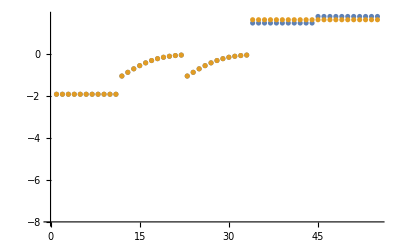

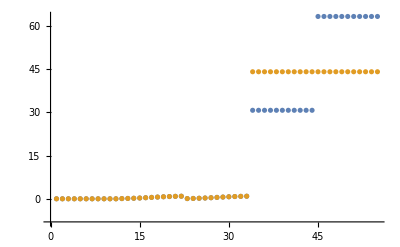

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

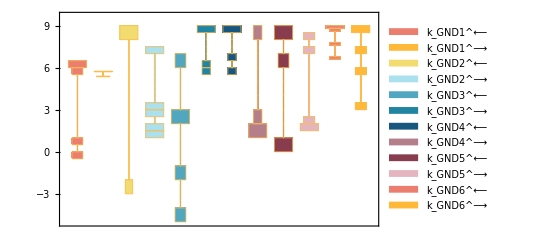

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

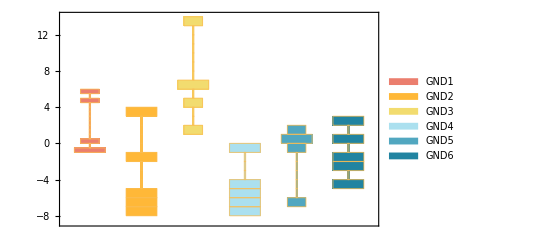

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

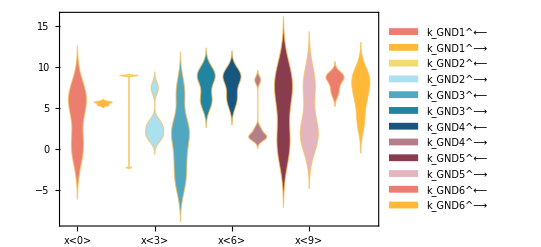

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

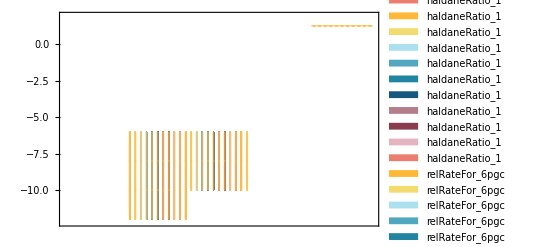

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,{{1,6pgc,0.000093,{0.00092,0.000094},{{nadp,0.002}},M,8,25,{{trishcl,0.05}},{{mg2,0.02},{cl,0.04}}},{1,nadp,0.000049,{0.000042,0.000056},{{6pgc,0.002}},M,8,25,{{trishcl,0.05}},{{mg2,0.02},{cl,0.04}}}},{((6pgc)^c k_GND1^⟶ (nadp^c k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ (k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶)+nadp^c k_GND3^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶)))))/(nadp^c k_GND2^⟶ k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND1^⟵ k_GND2^⟶ k_GND4^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+k_GND6^⟶))+(6pgc)^c k_GND1^⟶ (nadp^c k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ (k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶)+nadp^c k_GND3^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶))))),(nadp^c k_GND3^⟶ (k_GND2^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+(6pgc)^c k_GND1^⟶ (k_GND2^⟶ k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶))))/(nadp^c k_GND2^⟶ k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND1^⟵ k_GND2^⟶ k_GND4^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+k_GND6^⟶))+(6pgc)^c k_GND1^⟶ (nadp^c k_GND3^⟶ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND2^⟶ (k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶)+nadp^c k_GND3^⟶ (k_GND5^⟶ k_GND6^⟶+k_GND4^⟶ (k_GND5^⟵+k_GND5^⟶+k_GND6^⟶)))))},{(co2^c (k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) k_GND3^⟵ k_GND5^⟵+nadph^c k_GND4^⟵ (k_GND1^⟵ k_GND3^⟵ k_GND5^⟵+ru5p__D^c k_GND2^⟵ (k_GND3^⟵ k_GND5^⟵+k_GND1^⟵ (k_GND3^⟵+k_GND5^⟵+k_GND5^⟶)))) k_GND6^⟵)/(k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶))))),(nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶)))))/(k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶))))),(ru5p__D^c k_GND2^⟵ (co2^c nadph^c k_GND3^⟵ k_GND4^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND1^⟵ k_GND3^⟵ (co2^c k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND1^⟵ k_GND4^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶))))/(k_GND1^⟵ (ru5p__D^c k_GND2^⟵+k_GND2^⟶) (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND4^⟶ k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ k_GND4^⟶ (k_GND5^⟵+k_GND6^⟶))+nadph^c k_GND4^⟵ (co2^c k_GND1^⟵ k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+ru5p__D^c k_GND2^⟵ (co2^c k_GND3^⟵ k_GND5^⟵ k_GND6^⟵+k_GND1^⟵ (co2^c (k_GND5^⟵+k_GND5^⟶) k_GND6^⟵+k_GND5^⟶ k_GND6^⟶+k_GND3^⟵ (k_GND5^⟵+co2^c k_GND6^⟵+k_GND6^⟶)))))},{(6pgc)^c→∞,nadp^c→∞},{co2^c→∞,nadph^c→∞,ru5p__D^c→∞},{k_GND1^⟵→5.83733,k_GND1^⟶→236077.,k_GND2^⟵→7.78217×10^8,k_GND2^⟶→51.3768,k_GND3^⟵→103.251,k_GND3^⟶→1.56697×10^6,k_GND4^⟵→6.62102×10^8,k_GND4^⟶→2.61338×10^8,k_GND5^⟵→1.81229,k_GND5^⟶→40.4979,k_GND6^⟵→5.43416×10^7,k_GND6^⟶→1870.18},1,GND]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
30.7188 | (7.52369×10^26 nadp^c)/(2.10851×10^16+1.59348×10^21 nadp^c+236077. (3.10156×10^19 nadp^c+51.3768 (7.03063×10^13+7.83183×10^17 nadp^c))) | 3.25534 Abs[30.7188-(7.52369×10^26 nadp^c)/(2.10851×10^16+1.59348×10^21 nadp^c+236077. (3.10156×10^19 nadp^c+51.3768 (7.03063×10^13+7.83183×10^17 nadp^c)))]
63.2692 | (7.52369×10^26 (6pgc)^c)/(1.5935×10^21+1.68221×10^25 (6pgc)^c) | 1.58055 Abs[63.2692-(7.52369×10^26 (6pgc)^c)/(1.5935×10^21+1.68221×10^25 (6pgc)^c)]

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.0123 | 0.0123 | 0.000179966

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.0123 | 0.0123 | 0.000179966

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,0,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/haldaneRatio_1.txt,0.0123},{1,9.3×10^-6,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.0909091},{1,0.0000147395,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.136807},{1,0.0000233605,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.20076},{1,0.000037024,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.284747},{1,0.000058679,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.386863},{1,0.000093,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.5},{1,0.000147395,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.613137},{1,0.000233605,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.715253},{1,0.00037024,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.79924},{1,0.00058679,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.863193},{1,0.00093,0,0.002,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_6pgc.txt,0.909091},{1,0.002,0,4.9×10^-6,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.0909091},{1,0.002,0,7.76598×10^-6,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.136807},{1,0.002,0,0.0000123082,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.20076},{1,0.002,0,0.0000195073,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.284747},{1,0.002,0,0.0000309169,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.386863},{1,0.002,0,0.000049,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.5},{1,0.002,0,0.0000776598,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.613137},{1,0.002,0,0.000123082,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.715253},{1,0.002,0,0.000195073,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.79924},{1,0.002,0,0.000309169,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.863193},{1,0.002,0,0.00049,0,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/relRateFor_nadp.txt,0.909091},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,30.7188},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692},{1,0.01,0,0.01,0,0,1,8,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_GND_typeII/input/absRateFor.txt,63.2692}},{0.541549,{5.83733,236077.,7.78217×10^8,51.3768,103.251,1.56697×10^6,6.62102×10^8,2.61338×10^8,1.81229,40.4979,5.43416×10^7,1870.18},{0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0123,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857,44.0857}},{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.000437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.000694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.00437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.00694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.}},{1.15461×10^-22,{538.263,26248.2,1.50533×10^8,28.8607,194.069,9.19561×10^6},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.}},{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,GND,«20»,{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]